## Zestaw 10 1N

Katarzyna Sowa

Wykonano wykres calki ∫_0^(π/2) √(1-m^2 Sin[t]^2)ⅆt

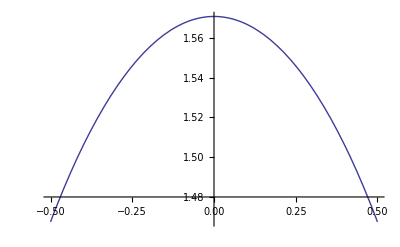

```mathematica
f[x_] = Integrate[Sqrt[1-x^2 Sin[t]^2],{t,0,π/2}];
Plot[f[x],{x,-0.5, 0.5}]
```

Obliczono przyblizenia Pade R_22,R_04 i R_13.

```mathematica
f[x_] = Integrate[Sqrt[1-x^2 Sin[t]^2],{t,0,π/2},GenerateConditions->False];
```

Jawne wzory na przyblizenia:

```mathematica
Pade[nn_]:=Module[{n=nn},
R22[x_] := N[PadeApproximant[f[x],{x,n,2}]];
R04[x_] :=N[PadeApproximant[R22[x],{x,n,{0,4}}]];
R13[x_] =N[PadeApproximant[R04[x],{x,n,{1,3}}]];
y=R22[x];
w=R04[x];
z=R13[x];
Print["Pierwsze przyblizenie = ",R22[x] ];
Print["Drugie przyblizenie = ",R04[x]];
Print["Trzecie przyblizenie = ", R13[x]];
Print["Wykresy funkcji (kolor czerwony) i jej przyblizen, odpowiednio: R_22 kolor niebieski, R_04 - czarny, R_13 - zielony."];
Show[Plot[f[x],{x,-0.5,0.5},PlotStyle->Red],
Plot[y,{x,-0.5,0.5},PlotStyle->Blue],
Plot[w,{x,-0.5,0.5},PlotStyle->Black],
Plot[z,{x,-0.5,0.5},PlotStyle->Green]]]
```

Pierwsze przyblizenie = (1.48008-0.504561 (-0.47+x)-1.21425 (-0.47+x)^2)/(1.-0.0674282 (-0.47+x)-0.488 (-0.47+x)^2)

Drugie przyblizenie = 1.48008/(1.+0.273473 (-0.47+x)+0.425625 (-0.47+x)^2+0.369453 (-0.47+x)^3+0.475129 (-0.47+x)^4)

Trzecie przyblizenie = (1.48008-1.90343 (-0.47+x))/(1.-1.01256 (-0.47+x)+0.0739291 (-0.47+x)^2-0.177914 (-0.47+x)^3)

Wykresy funkcji (kolor czerwony) i jej przyblizen, odpowiednio: R_22 kolor niebieski, R_04 - czarny, R_13 - zielony.

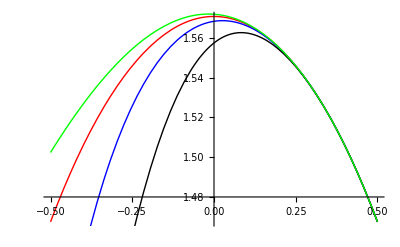

```mathematica
Pade[0.47]
```